```mathematica
data = Import[NotebookDirectory[]<>"../treni/links.csv", "CSV"];
```

```mathematica
g = Graph[#1 ->#2 &@@@ data, VertexLabels->Automatic, EdgeWeight->(#1 ->#2->#3 &@@@ data)];
```

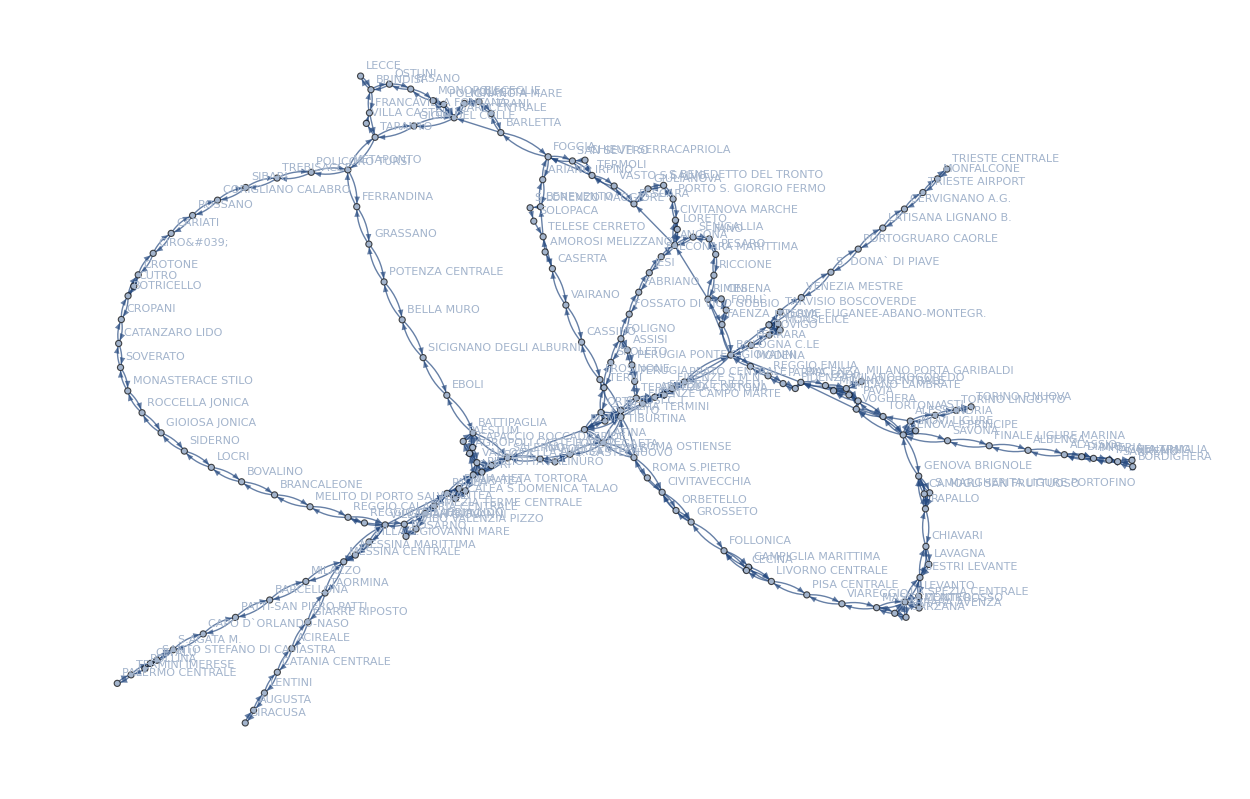

```mathematica
GraphPlot[g]
```

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {0.6.5}

System`PacletInstall::samevers: A paclet named IGraphM with the same version number (0.6.5) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

Installation failed. Please install IGraph/M manually. https://github.com/szhorvat/IGraphM#installation

```mathematica
<<IGraphM`
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

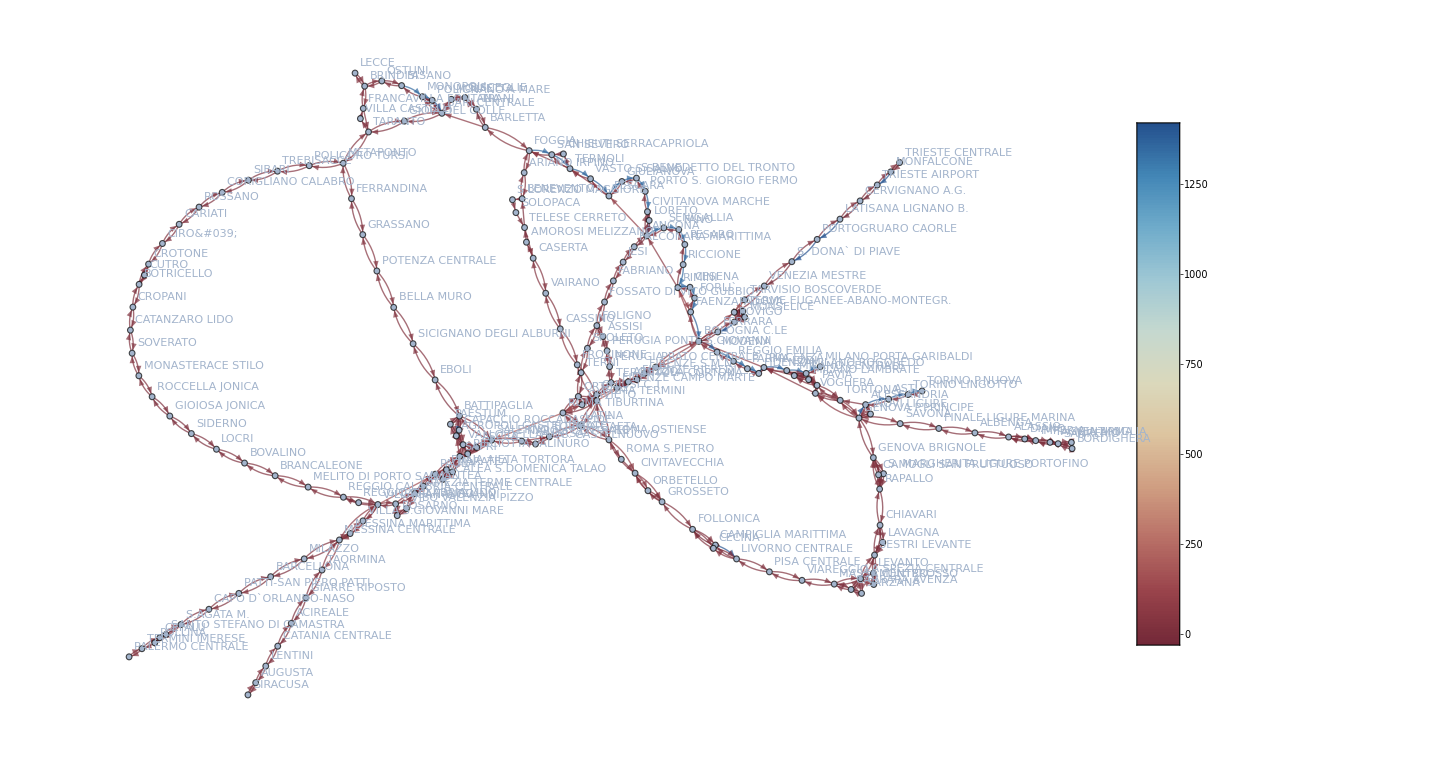

```mathematica
Legended[IGEdgeMap[ColorData["RedBlueTones"],EdgeStyle->Rescale@*IGEdgeProp[EdgeWeight],g],BarLegend[{"RedBlueTones",MinMax@IGEdgeProp[EdgeWeight][g]}]]
```

```mathematica
coords=GraphEmbedding[g,"SpringElectricalEmbedding", 3];
Graphics3D[GraphicsComplex[coords,{Table[Sphere[VertexIndex[g,v],.1],{v,VertexList[g]}],Table[Tube[{VertexIndex[g,First[e]],VertexIndex[g,Last[e]]},.03],{e,EdgeList[g]}]}],Boxed->True]
```

-Graphics3D-

```mathematica
VertexCount[g]
```

207